### Wprowadzenie wartości dla masy samochodu ( "m" ), przyspieszenia ziemskiego ( "g" ) i promienia koła samochodu ( "r" ).

```mathematica
ClearAll["Global`*"];
Off[Solve::incnst];
```

```mathematica
m=1000;     (* kg *)
```

```mathematica
g=9.81;       (* m/s^2 *)
```

### Zdefiniowanie procedury "A[k_, μ_]". Wyznacza ona zależność drogi ( "x[t]" ) od czasu ( "t" ) poprzez rozwiązanie równania ruchu uwzględniającego opór powietrza (symbol "k" oznacza współczynnik proporcjonalności siły oporu powietrza do kwadratu prędkości samochodu) i tarcie opon o podłoże (symbol "μ" oznacza współczynnik tarcia poślizgowego).

```mathematica
A[k_,μ_]:=NDSolve[{m×D[x[t], t,t]==-k×(D[x[t], t])^2-μ×m×g×UnitStep[D[x[t], t]],D[x[t], t]==25/.t->0,x[0]==0},x[t],{t,0,10}]
```

### Wywołanie procedury "A[k_, μ_]" dla czterech kombinacji współczynników "k" i "μ" i zapisanie wyników w macierzy “rozw”.

```mathematica
rozw=Outer[A,{2,4},{0.6,0.3}];
```

### Wyznaczenie zależności drogi ( "x_(i,j)[t]" ) od czasu ( "t" ) dla czterech rozwiązań równania ruchu.

```mathematica
Do[x[i,j]=x[t]/.rozw[[i,j]],{i,1,2},{j,1,2}]
```

### Wyznaczenie zależności prędkości ( "v_(i,j)[t]" ) od czasu ( "t" ) dla czterech rozwiązań równania ruchu.

```mathematica
Do[v[i,j]=D[x[i,j], t],{i,1,2},{j,1,2}]
```

### Sporządzenie wykresu obrazującego zależność prędkości samochodu od czasu dla k = 2 [kg/m] i dwóch wartości współczynnika tarcia poślizgowego.

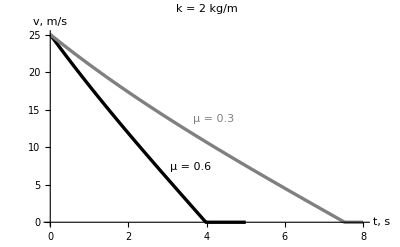

```mathematica
rys1=Plot[Evaluate[v[1,1]],{t,0,5},PlotRange->All,
PlotStyle->{Black,Thickness[0.006]}];

 rys2=Plot[Evaluate[v[1,2]],{t,0,8},PlotRange->All,
PlotStyle->{Gray,Thickness[0.006]}];

Show[rys1,rys2,
BasStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{ "t, s","v, m/s"},
PlotLabel->StyleForm[" k = 2 kg/m",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
Prolog->{Text[StyleForm["μ = 0.6",FontColor->Black],Scaled[{0.45,0.3}]],
Text[StyleForm["μ = 0.3  ",FontColor->Gray],Scaled[{0.52,0.55}]]}]
```

### Sporządzenie wykresu obrazującego zależność prędkości samochodu od czasu dla k = 4 [kg/m] i dwóch wartości współczynnika tarcia poślizgowego.

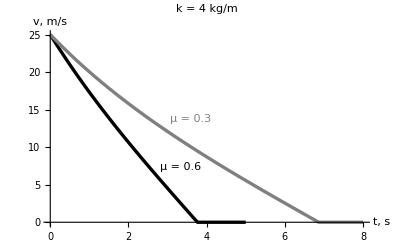

```mathematica
rys3=Plot[Evaluate[v[2,1]],{t,0,5},PlotRange->All,
PlotStyle->{Black,Thickness[0.006]}];

 rys4=Plot[Evaluate[v[2,2]],{t,0,8},PlotRange->All,
PlotStyle->{Gray,Thickness[0.006]}];

Show[rys3,rys4,
Basetyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{ "t, s","v, m/s"},
PlotLabel->StyleForm[" k = 4 kg/m",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
Prolog->{Text[StyleForm["μ = 0.6",FontColor->Black],Scaled[{0.42,0.3}]],
Text[StyleForm["μ = 0.3  ",FontColor->Gray],Scaled[{0.45,0.55}]]}]
```

### Sporządzenie wykresu obrazującego zależność drogi jaką przebywa samochód podczas hamowania od czasu dla k = 2 [kg/m] i dwóch wartości współczynnika tarcia poślizgowego.

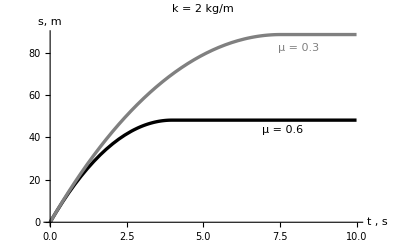

```mathematica
rys5=Plot[Evaluate[x[1,1]],{t,0,10},PlotRange->All,
PlotStyle->{Black,Thickness[0.006]}];

 rys6=Plot[Evaluate[x[1,2]],{t,0,10},PlotRange->All,
PlotStyle->{Gray,Thickness[0.006]}];

Show[rys5,rys6,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{ "t , s","s, m"},
PlotLabel->StyleForm[" k = 2 kg/m",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
Prolog->{Text[StyleForm["μ = 0.6",FontColor->Black],Scaled[{0.75,0.49}]],
Text[StyleForm["μ = 0.3  ",FontColor->Gray],Scaled[{0.80,0.91}]]}]
```

### Sporządzenie wykresu obrazującego zależność drogi jaką przebywa samochód podczas hamowania od czasu dla k = 4 [kg/m] i dwóch wartości współczynnika tarcia poślizgowego.

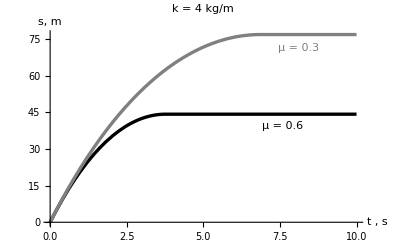

```mathematica
rys7=Plot[Evaluate[x[2,1]],{t,0,10},PlotRange->All,
PlotStyle->{Black,Thickness[0.006]}];

 rys8=Plot[Evaluate[x[2,2]],{t,0,10},PlotRange->All,
PlotStyle->{Gray,Thickness[0.006]}];

Show[rys7,rys8,
BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
AxesLabel->{ "t , s","s, m"},
PlotLabel->StyleForm[" k = 4 kg/m",FontFamily->"Helvetica",FontSlant->"Plain",
FontWeight ->"Bold",FontSize->12],
Prolog->{Text[StyleForm["μ = 0.6",FontColor->Black],Scaled[{0.75,0.51}]],
Text[StyleForm["μ = 0.3  ",FontColor->Gray],Scaled[{0.80,0.91}]]}]
```